```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Tru_Tm.txt","Table"];
```

```mathematica
size=Dimensions[mp0][[1]]
α=Log[mp0[[2,1]]/mp0[[1,1]]]/Log[mp0[[2,2]]/mp0[[1,2]]]
β=Log[mp0[[size,2]]/mp0[[size-1,2]]]/Log[mp0[[size,1]]/mp0[[size-1,1]]]
```

496

1.03608

-2.44708

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Dimensions[trlist]
```

{140,2}

```mathematica
Pmgood[k_]=If[k<0.0001||k>1.993,0,Pm[k]]
```

If[k<0.0001||k>1.993,0,Pm[k]]

```mathematica
Plot[(1+r^2)/(2r),{r,0,5}];
```

```mathematica
Limit[(r-μ)/(1+r^2-2r*μ)^(1/2),r->1]/.μ->1
```

0

```mathematica
Limit[(3r+7μ-10r*μ^2)/(14*r*(1+r^2-2r*μ)),r->1]/.μ->1
```

13/28

```mathematica
Clear[S]
S=#^3/(2*Pi^2)*(fgps[#,Pmgood]-fgps2[#,Pmgood])&/@Take[trlist,{1,140,1}][[All,1]]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

Suave::success: Needed 50111 function evaluations on 50 subregions.

Suave::success: Needed 1000 function evaluations on 1 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

{-5.75063×10^-8,-9.11416×10^-8,-1.44458×10^-7,-2.28792×10^-7,-3.62627×10^-7,-5.75×10^-7,-9.11075×10^-7,-1.44261×10^-6,-2.28927×10^-6,-3.62461×10^-6,-5.74612×10^-6,-9.11574×10^-6,-0.0000144401,-0.0000228735,-0.0000362438,-0.0000574786,-0.0000911304,-0.000144444,-0.000228755,-0.0003628,-0.000574701,-0.00091103,-0.00144359,-0.00228819,-0.00362701,-0.00574727,-0.00910874,-0.0144359,-0.0228876,-0.0362666,-0.0574773,-0.0910947,-0.144368,-0.22884,-0.36268,-0.574644,-0.910672,-1.44294,-2.2872,-3.62195,-5.72797,-9.05016,-14.2501,-22.3217,-34.6407,-52.9543,-79.0183,-113.92,-156.065,-200.097,-236.623,-257.322,-254.646,-226.543,-189.194,-157.142,-126.409,-94.8772,-61.5543,-25.7811,11.7816,50.4047,89.2566,127.223,163.835,198.03,229.48,257.336,281.59,303.52,323.274,342.006,359.867,377.842,396.777,418.188,441.35,466.389,492.897,519.393,545.299,567.894,587.412,602.095,614.209,623.559,631.966,640.827,650.111,662.037,674.662,685.895,696.369,702.053,705.418,706.145,705.921,706.335,707.41,708.72,708.745,707.142,702.924,697.544,691.54,685.758,680.189,673.182,664.581,655.12,645.611,635.55,625.181,613.458,601.119,588.157,574.628,560.309,545.059,528.922,512.204,493.533,473.601,451.801,427.639,400.61,368.459,328.719,278.548,218.518,159.873,113.489,25.8476,4.17539,0.,0.,0.,0.,0.,0.}

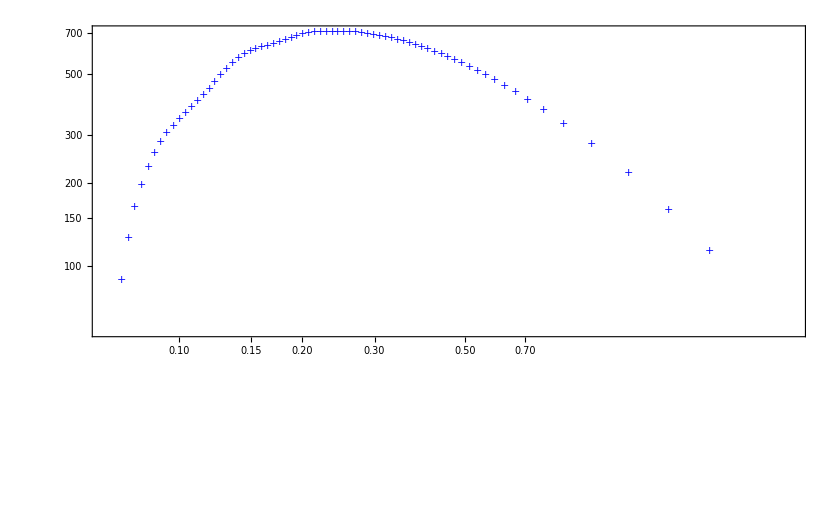

```mathematica
ListLogLogPlot[Thread[{Take[trlist[[All,1]],{1,140,1}],S}],Frame->True,PlotStyle->{Thick,Blue},PlotMarkers->"+"]
```